### From Preston’s code

```mathematica
SetOptions[Plot,Axes->False,Frame->{True,True,False,False},LabelStyle->Directive[Black, 16],ImageSize->Medium];
SetOptions[ListPlot,Axes->False,Frame->{True,True,False,False},LabelStyle->Directive[Black, 15],ImageSize->Medium];

μ0 = 4π*10^-7;
cm = 100;
mm = 1000;

(*field in z from circular coil. SI units*)
BzCircCoil[r_,z_,length_,radius_,turns_,amps_]:=Module[{L=length,a=radius,t=turns,i=amps,n,B0,ζ1,ζ2,m1,m2,u},
n = t/L;
B0 = μ0 i n;
u = (4a r)/(a+r)^2;
ζ1 = z+L/2;
ζ2 = z-L/2;
m1 = (4 a r)/((a+r)^2+ζ1^2);
m2 = (4 a r)/((a+r)^2+ζ2^2);
B0/(4π)1/(√(a r))(√m1 ζ1(EllipticK[m1]+((a-r)/(a+r))EllipticPi[u,m1])-√m2 ζ2(EllipticK[m2]+((a-r)/(a+r))EllipticPi[u,m2]))
];
(*field in r from circular coil. SI units*)
BrCircCoil[r_,z_,length_,radius_,turns_,amps_]:=Module[{L=length,a=radius,t=turns,i=amps,n,B0,ζ1,ζ2,m1,m2},
n = t/L;
B0 = μ0 i n;
ζ1 = z+L/2;
ζ2 = z-L/2;
m1 = (4 a r)/((a+r)^2+ζ1^2);
m2 = (4 a r)/((a+r)^2+ζ2^2);
B0/π √(a/r)(1/(√m1)(EllipticE[m1]-(1-m1/2)EllipticK[m1])-1/(√m2)(EllipticE[m2]-(1-m2/2)EllipticK[m2]))
];
BxRectCoil[x_,y_,z_,length_,wx_,wy_,turns_,amps_]:=Module[{L=length,ax=wx/2,ay=wy/2,az=L/2,n=turns/length,B0,rijk,i,j,k},
B0 = μ0 amps n;
rijk = √((x+ax(-1)^(i+1))^2+(y+ay(-1)^(j+1))^2+(z+az(-1)^(k+1))^2);
 B0/(8π)Sum[(-1)^(i+j+k)Log[(-(y+ay(-1)^(j+1))+rijk)/(y+ay(-1)^(j+1)+rijk)],{i,{0,1}},{j,{0,1}},{k,{0,1}}]
];
ByRectCoil[x_,y_,z_,length_,wx_,wy_,turns_,amps_]:=Module[{L=length,ax=wx/2,ay=wy/2,az=L/2,n=turns/length,B0,rijk,i,j,k},
B0 = μ0 amps n;
rijk = √((x+ax(-1)^(i+1))^2+(y+ay(-1)^(j+1))^2+(z+az(-1)^(k+1))^2);
B0/(8π)Sum[(-1)^(i+j+k)Log[(-(x+ax(-1)^(i+1))+rijk)/(x+ax(-1)^(i+1)+rijk)],{i,{0,1}},{j,{0,1}},{k,{0,1}}]
];
BzRectCoil[x_,y_,z_,length_,wx_,wy_,turns_,amps_]:=Module[{L=length,ax=wx/2,ay=wy/2,az=L/2,n=turns/length,B0,rijk,i,j,k},
B0=μ0 amps n;
rijk = √((x+ax(-1)^(i+1))^2+(y+ay(-1)^(j+1))^2+(z+az(-1)^(k+1))^2);
B0/(4π)Sum[(-1)^(i+j+k+1)(ArcTan[((x+ax(-1)^(i+1))(z+az(-1)^(k+1)))/((y+ay(-1)^(j+1))rijk)]+ArcTan[((y+ay(-1)^(j+1))(z+az(-1)^(k+1)))/((x+ax(-1)^(i+1))rijk)]),{i,{0,1}},{j,{0,1}},{k,{0,1}}]
];
```

```mathematica
(*X,Y SHIM*)
Clear[dia]
(*independent variables*)
L=0.01;(*length, m*)
wx= 0.1097;(*x width, m*)
wy= 0.066;(*y width, m*)
dia=0.65/mm; (*wire dia, mm*)
"coil turns (length)"
t=Floor[L/dia+0.5](*turns*)
amps=1;
"coil layers (thickness)"
layers = 4
"coil thickness [mm]"
dia*layers*mm
"coil length"
L*mm
d=wx;
(*d=0.150;*)(*coil separation, m*)
Bx=By=Bz=0;
Bxlist =Bylist=Bzlist= {};
(*construct the field from a pair of multi-layer coils*)
For[i=1,i<layers+1,i++,
(*Bz+=(BzRectCoil[x,y,z+d/2,L,wx+2(i-1)dia,wy+2(i-1)dia,t,amps]+BzRectCoil[x,y,z-d/2,L,wx+2(i-1)dia,wy+2(i-1)dia,t,amps]*4/3)*1.6/2.6;*)
Bz+=BzRectCoil[x,y,z+d/2,L,wx+2(i-1)dia,wy+2(i-1)dia,t,amps]+BzRectCoil[x,y,z-d/2,L,wx+2(i-1)dia,wy+2(i-1)dia,t,amps];
]
Print["Peak shim field [G] with ", amps," amps"]
10^4 Bz/.{x->0,y->0,z->0}

(*Theory1*)
theory1=Plot[10^4 Bz/.{x->0,y->0,z->zcm/cm},{zcm,-cm 1.2d/2,cm 1.2d/2},GridLines->{{{cm(d-L)/2,Thick},{cm(d+L)/2,Thick},{-cm(d-L)/2,Thick},{-cm(d+L)/2,Thick}},{0}},PlotRange->All,FrameLabel->{"z [cm]", "Bz [G]"},PlotLabel->"X/Y shim rectangular coils
"];

amps = -1;
Bx=By=Bz=0;
Bxlist =Bylist=Bzlist= {};
(*construct the field from a pair of multi-layer coils*)
For[i=1,i<layers+1,i++,
(*Bz+=(BzRectCoil[x,y,z+d/2,L,wx+2(i-1)dia,wy+2(i-1)dia,t,amps]+BzRectCoil[x,y,z-d/2,L,wx+2(i-1)dia,wy+2(i-1)dia,t,amps]*4/3)*1.6/2.6;*)
Bz+=BzRectCoil[x,y,z+d/2,L,wx+2(i-1)dia,wy+2(i-1)dia,t,amps]+BzRectCoil[x,y,z-d/2,L,wx+2(i-1)dia,wy+2(i-1)dia,t,amps];
]
Print["Peak shim field [G] with ", amps," amps"]
10^4 Bz/.{x->0,y->0,z->0}

(*Theory2*)
theory2=Plot[10^4 Bz/.{x->0,y->0,z->zcm/cm},{zcm,-cm 1.2d/2,cm 1.2d/2},GridLines->{{{cm(d-L)/2,Thick},{cm(d+L)/2,Thick},{-cm(d-L)/2,Thick},{-cm(d+L)/2,Thick}},{0}},PlotRange->All,FrameLabel->{"z [cm]", "Bz [G]"},PlotLabel->"X/Y shim rectangular coils
"];
```

coil turns (length)

15

coil layers (thickness)

4

coil thickness [mm]

2.6

coil length

10.

Peak shim field [G] with 1 amps

4.32313

Peak shim field [G] with -1 amps

-4.32313

### Experimental Data Rect X shim

```mathematica
minus1 = {{6.5,10.33},{6,10.22},{5.5,9.8},{5,9.19},{4.5,8.38},{4,7.6},{3.5,6.93},{3,6.25},{2.5,5.7},{2,5.24},{1.5,4.9},{1,4.66},{0.5,4.57},{0,4.55},{-0.5,4.64},{-1,4.83},{-1.5,5.14},{-2,5.6},{-2.5,6.1},{-3,6.73},{-3.5,7.47},{-4,8.13},{-4.5,8.8},{-5,9.35},{-5.5,9.66},{-6,9.63}};
plus1 = {{6.5,-10.4},{6,-10.22},{5.5,-9.8},{5,-9.12},{4.5,-8.4},{4,-7.59},{3.5,-6.87},{3,-6.22},{2.5,-5.63},{2,-5.23},{1.5,-4.89},{1,-4.64},{0.5,-4.55},{0,-4.5},{-0.5,-4.6},{-1,-4.85},{-1.5,-5.12},{-2,-5.5},{-2.5,-6},{-3,-6.7},{-3.5,-7.4},{-4,-8.2},{-4.5,-8.87},{-5,-9.4},{-5.5,-9.7},{-6,-9.64}};

minus1[[All,1]]=minus1[[All,1]]-0.2;
plus1[[All,1]]=plus1[[All,1]]-0.2;
A1 = ListPlot[minus1,PlotRange->{{-7,7},{0,10}}];
A2 = ListPlot[plus1,PlotRange->{{-7,7},{-10,0}}];
AmptoGauss = {{0,0.02},{0.1,-0.42},{0.2,-0.87},{0.3,-1.32},{0.4,-1.77},{0.5,-2.24},{0.6,-2.72},{0.7,-3.15},{0.8,-3.6},{0.9,-4},{1,-4.5},{1.1,-4.97},{1.2,-5.42},{1.3,-5.87},{1.4,-6.3},{1.5,-6.78},{1.6,-7.2},{1.7,-7.7},{1.8,-8.15},{1.9,-8.6},{2,-9},{2.1,-9.54},{2.2,-9.9},{2.3,-10.45},{2.4,-10.9},{2.5,-11.34},{2.6,-11.8},{2.7,12.26},{2.8,-12.7},{2.9,-13.19},{3,-13.63}};
AG = ListPlot[AmptoGauss, PlotRange->{{0,3},{-15,0.3}}];
```

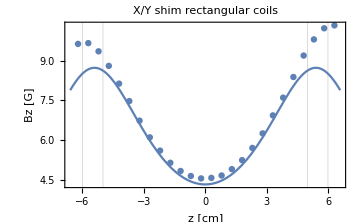

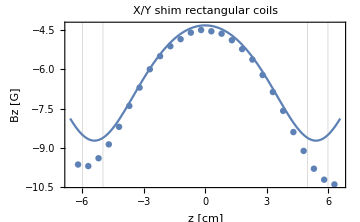

```mathematica
Show[theory1,A1]
Show[theory2,A2]
```

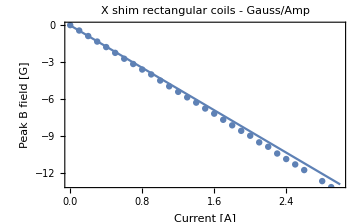

```mathematica
Clear[amps]
Bz=0;
For[i=1,i<layers+1,i++,
Bz+=BzRectCoil[x,y,z+d/2,L,wx+2(i-1)dia,wy+2(i-1)dia,t,amps]+BzRectCoil[x,y,z-d/2,L,wx+2(i-1)dia,wy+2(i-1)dia,t,amps];
]
theory3=Plot[-10^4 Bz/.{x->0,y->0,z->0},{amps,0,3},FrameLabel->{"Current [A]", "Peak B field [G]"},PlotLabel->"X shim rectangular coils - Gauss/Amp"];
Show[theory3,AG]
```

### Experimental Data Rect Y shim

Current on the horizontal axes refers to current per coil, i.e. each coil is being driven with the value on the horizontal axis to get the B field on the vertical axis.

```mathematica
minus1 = {{22,-9.4},{21.5,-9.1},{21,-8.55},{20.5,-7.85},{20,-7.17},{19.5,-6.1},{19,-5.84},{18.5,-5.35},{18,-4.92},{17.5,-4.62},{17,-4.41},{16.5,-4.32},{16,-4.32},{15.5,-4.4},{15,-4.61},{14.5,-4.93},{14,-5.35},{13.5,-5.88},{13,-6.53},{12.5,-7.13},{12,-8},{11.5,-8.77},{11,-9.46},{10.5,-9.93}};
plus1 = {{22,9.5},{21.5,9.2},{21,8.6},{20.5,7.94},{20,8.19},{19.5,6.45},{19,5.88},{18.5,5.36},{18,4.96},{17.5,4.66},{17,4.46},{16.5,4.36},{16,4.36},{15.5,4.45},{15,4.67},{14.5,4.96},{14,5.4},{13.5,5.97},{13,6.55},{12.5,7.34},{12,8.09},{11.5,8.89},{11,9.52},{10.5,10.01}};

minus1[[All,1]]=minus1[[All,1]]-16.2;
plus1[[All,1]]=plus1[[All,1]]-16.2;
A1 = ListPlot[minus1,PlotRange->{{-7,7},{0,10}}];
A2 = ListPlot[plus1,PlotRange->{{-7,7},{-10,0}}];
AmptoGauss = {{0,0.03},{0.2,0.87},{0.4,1.73},{0.6,2.61},{0.8,3.47},{1,4.33},{1.2,5.23},{1.4,6.05},{1.6,6.91},{1.8,7.82},{2,8.7},{2.2,9.55},{2.4,10.4},{2.6,11.25},{2.8,12.1},{3,13}};
AG = ListPlot[AmptoGauss, PlotRange->{{0,3},{-15,0.3}}];
```

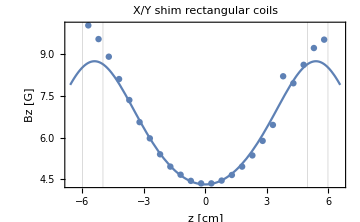

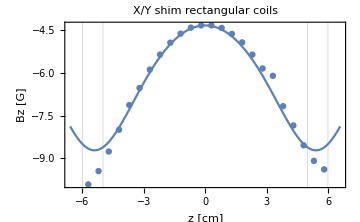

```mathematica
Show[theory1,A2]
Show[theory2,A1]
```

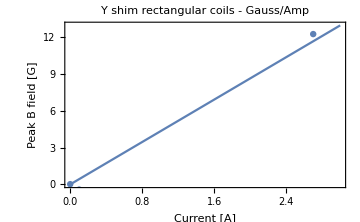

```mathematica
Clear[amps]
Bz=0;
For[i=1,i<layers+1,i++,
Bz+=BzRectCoil[x,y,z+d/2,L,wx+2(i-1)dia,wy+2(i-1)dia,t,amps]+BzRectCoil[x,y,z-d/2,L,wx+2(i-1)dia,wy+2(i-1)dia,t,amps];
]
theory3=Plot[10^4 Bz/.{x->0,y->0,z->0},{amps,0,3},FrameLabel->{"Current [A]", "Peak B field [G]"},PlotLabel->"Y shim rectangular coils - Gauss/Amp"];
Show[theory3,AG]
```

```mathematica
mm = 10^-3;
m = 1;
diameter = 0.65 *mm;
area = (diameter/2)^2*π;
length = 10 * m;
resistivity = 1.72*10^-8(*@ 20C*);
Resistance = resistivity * length / area;
Print["Resistance at 20C = ", Resistance]
```

Resistance at 20C = 0.518337

```mathematica
temp = 50;
Print["Resistance at ",temp,"C = ", Resistance + 0.00386*(temp-20)]
```

Resistance at 50C = 0.634137